```mathematica
(*Exit[];*)
```

```mathematica
NotebookDelete/@Select[Cells[GeneratedCell->False],StringMatchQ[First@FrontEndExecute[FrontEnd`ExportPacket[NotebookRead@#,"InputText"]],(" "|"\t"|"\r"|"\n"|"
")...]&];
ClearMemory:=Module[{},Unprotect[In,Out];
Clear[In,Out];
Protect[In,Out];
ClearSystemCache[];];
```

```mathematica
temp=Import[NotebookDirectory[]<>"../output/unique_bjorken_yield.dat","Table"];
```

```mathematica
Print[Take[temp,5]]
```

{{#,mT,pT,phi_p,y_p,dNd3p,dNd3p,(GeV^{-3})},{0.13957,0.,0.,0.,0.0119908,1.56059},{0.33997,0.31,0.,0.,0.00613298,0.798199},{0.635515,0.62,0.,0.,0.00216737,0.28208},{0.635515,0.62,0.,0.,0.00146716,0.190948}}

```mathematica
labels = First[temp][[2;;6]]
points=Rest[temp];
structuredData={#[[1]],#[[6]]}&/@points;
Print[Take[structuredData,5]](*Print the first 5 structured data points*)


localYield=Interpolation[structuredData]
```

{mT,pT,phi_p,y_p,dNd3p}

{{0.13957,1.56059},{0.33997,0.798199},{0.635515,0.28208},{0.635515,0.190948},{0.635515,0.333865}}

Interpolation::inddp: The point 0.635515 in dimension 1 is duplicated.

Interpolation[{{0.13957,1.56059},{0.33997,0.798199},{0.635515,0.28208},{0.635515,0.190948},{0.635515,0.333865},{0.635515,0.338815},{0.635515,0.261988},{0.635515,0.340466},{0.635515,0.338815},{0.940415,0.0375273},{1.24783,0.00687043},{1.24783,0.010225},{1.24783,0.00687043},{1.24783,0.00812371},{1.24783,0.010225},{1.24783,0.00926044},{1.24783,0.00812371},{1.24783,0.00812371},{1.55627,0.00206544},{1.55627,0.00206544},{1.55627,0.00206544},{1.55627,0.00121413},{1.55627,0.00167405},{1.55627,0.00206544},{1.55627,0.0014585},{1.55627,0.00206544},{1.86523,0.000209944},{2.17448,0.000050936},{2.17448,0.0000357636},{2.48392,6.0256×10^-6},{2.79349,1.00668×10^-6},{3.10314,2.85912×10^-7},{3.10314,1.67062×10^-7},{3.10314,2.85912×10^-7},{3.41286,2.75741×10^-8},{3.72262,4.53071×10^-9},{4.03242,1.10622×10^-9},{4.03242,1.23924×10^-9},{4.03242,1.10622×10^-9},{4.03242,7.41619×10^-10},{4.03242,1.10622×10^-9},{4.03242,7.41619×10^-10},{4.03242,1.22682×10^-9},{4.34224,1.21×10^-10},{4.34224,2.01495×10^-10},{4.34224,2.01562×10^-10},{4.65209,1.96865×10^-11},{4.65209,3.25456×10^-11},{4.65209,2.95594×10^-11},{4.65209,2.56085×10^-11},{4.96196,3.1951×10^-12},{4.96196,4.1737×10^-12},{4.96196,4.1737×10^-12},{4.96196,4.8086×10^-12},{5.27185,7.801×10^-13},{5.27185,6.785×10^-13},{5.27185,5.174×10^-13},{5.27185,8.471×10^-13},{5.27185,8.472×10^-13},{5.58175,1.362×10^-13},{5.58175,8.36×10^-14},{5.89165,1.35×10^-14},{6.20157,2.2×10^-15},{6.20157,2.2×10^-15},{6.20157,2.2×10^-15},{6.20157,2.2×10^-15}}]

```mathematica
Print[Take[points,5]]
```

{{0.13957,0.,0.,0.,0.0119908,1.56059},{0.33997,0.31,0.,0.,0.00613298,0.798199},{0.635515,0.62,0.,0.,0.00146716,0.190948},{1.24783,1.24,0.,0.,0.0000785636,0.010225},{1.55627,1.55,0.,0.,9.3288×10^-6,0.00121413}}

```mathematica
structuredData2={#[[1;;3]],#[[4]]}&/@points;
Print[Take[structuredData2,5]]
```

{{{0.13957,0.,0.},0.},{{0.33997,0.31,0.},0.},{{0.635515,0.62,0.},0.},{{1.24783,1.24,0.},0.},{{1.55627,1.55,0.},0.}}

```mathematica
structuredData[[1]]
```

{{0.13957,0.,0.},0.0119908}

```mathematica
localYield[0,0,-1]
```

Interpolation[{{{0.13957,0.,0.},0.0119908},{{0.33997,0.31,0.},0.00613298},{{0.635515,0.62,0.},0.00146716},{{1.24783,1.24,0.},0.0000785636},{{1.55627,1.55,0.},9.3288×10^-6},{{1.24783,1.24,0.},0.0000951314},{{4.96196,4.96,0.},3.21×10^-14},{{5.58175,5.58,0.},1.×10^-15},{{4.96196,4.96,0.},4.04×10^-14},{{6.20157,6.2,0.},0.},{{0.635515,0.62,0.},0.00250199},{{0.940415,0.93,0.},0.000288342},{{1.24783,1.24,0.},0.000052789},{{4.96196,4.96,0.},3.21×10^-14},{{6.20157,6.2,0.},0.},{{1.55627,1.55,0.},0.0000158698},{{1.86523,1.86,0.},1.61311×10^-6},{{2.17448,2.17,0.},2.7479×10^-7},{{4.03242,4.03,0.},7.3408×10^-12},{{3.72262,3.72,0.},5.84783×10^-11},{{4.65209,4.65,0.},2.504×10^-13},{{5.27185,5.27,0.},6.4×10^-15},{{4.96196,4.96,0.},4.02×10^-14},{{6.20157,6.2,0.},0.},{{2.17448,2.17,0.},3.91368×10^-7},{{2.48392,2.48,0.},4.62978×10^-8},{{2.79349,2.79,0.},7.73485×10^-9},{{3.10314,3.1,0.},1.28362×10^-9},{{3.72262,3.72,0.},5.77648×10^-11},{{4.03242,4.03,0.},5.6982×10^-12},{{3.72262,3.72,0.},5.87401×10^-11},{{4.65209,4.65,0.},2.504×10^-13},{{5.27185,5.27,0.},6.4×10^-15},{{5.58175,5.58,0.},6.×10^-16},{{4.96196,4.96,0.},4.04×10^-14},{{6.20157,6.2,0.},0.},{{3.10314,3.1,0.},2.19681×10^-9},{{3.41286,3.41,0.},2.11866×10^-10},{{3.72262,3.72,0.},3.48118×10^-11},{{4.65209,4.65,0.},2.505×10^-13},{{5.27185,5.27,0.},6.5×10^-15},{{4.96196,4.96,0.},4.04×10^-14},{{6.20157,6.2,0.},0.},{{4.03242,4.03,0.},8.4996×10^-12},{{4.34224,4.34,0.},9.297×10^-13},{{4.65209,4.65,0.},1.513×10^-13},{{4.96196,4.96,0.},2.45×10^-14},{{5.27185,5.27,0.},4.×10^-15},{{4.96196,4.96,0.},4.04×10^-14},{{6.20157,6.2,0.},0.},{{4.65209,4.65,0.},2.501×10^-13},{{4.96196,4.96,0.},2.45×10^-14},{{6.20157,6.2,0.},0.},{{5.58175,5.58,0.},1.×10^-15},{{5.89165,5.89,0.},1.×10^-16},{{6.20157,6.2,0.},0.}}][0,0,-1]

```mathematica
dNd3p[pT_,phi_,y_]:=localYield[pT,phi,y]
```

```mathematica
Plot[dNd3p[pT,0,0],{pT,0,1}]
```

-Graphics-

```mathematica
vol=NIntegrate[dNd3p[pT,phi,y]pT^2,{phi,0,2Pi},{pT,0,6.2},{y,-1,1}];
```

NIntegrate::inumr: The integrand pT^2 Interpolation[{{{0.13957,0.,0.},0.0119908},{{0.33997,0.31,0.},0.00613298},{{0.635515,0.62,0.},0.00146716},{{1.24783,1.24,0.},0.0000785636},{{1.55627,1.55,0.},9.3288×10^-6},{{1.24783,1.24,0.},0.0000951314},{{4.96196,4.96,0.},3.21×10^-14},{{5.58175,5.58,0.},1.×10^-15},{{4.96196,4.96,0.},4.04×10^-14},{{6.20157,6.2,0.},0.},«46»}][pT,phi,y] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,6.28319},{0,6.2},{-1,1}}.

```mathematica
dNdy[y_]:=NIntegrate[dNd3p[pT,phi,y]pT^2,{phi,0,2Pi},{pT,0,6.2}]
```

```mathematica
dNdP[pT_]:=NIntegrate[dNd3p[pT,phi,y],{phi,0,2Pi},{y,-1,1}]
```

```mathematica
vol
```

NIntegrate::inumr: The integrand pT^2 Interpolation[{{{0.13957,0.,0.},0.0119908},{{0.33997,0.31,0.},0.00613298},{{0.635515,0.62,0.},0.00146716},{{1.24783,1.24,0.},0.0000785636},{{1.55627,1.55,0.},9.3288×10^-6},{{1.24783,1.24,0.},0.0000951314},{{4.96196,4.96,0.},3.21×10^-14},{{5.58175,5.58,0.},1.×10^-15},{{4.96196,4.96,0.},4.04×10^-14},{{6.20157,6.2,0.},0.},«46»}][pT,phi,y] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,6.28319},{0,6.2},{-1,1}}.

NIntegrate[dNd3p[pT,phi,y] pT^2,{phi,0,2 π},{pT,0,6.2},{y,-1,1}]

```mathematica
dNdy[0.001]
```

NIntegrate::inumr: The integrand pT^2 Interpolation[{{{0.13957,0.,0.},0.0119908},{{0.33997,0.31,0.},0.00613298},{{0.635515,0.62,0.},0.00146716},{{1.24783,1.24,0.},0.0000785636},{{1.55627,1.55,0.},9.3288×10^-6},{{1.24783,1.24,0.},0.0000951314},{{4.96196,4.96,0.},3.21×10^-14},{{5.58175,5.58,0.},1.×10^-15},{{4.96196,4.96,0.},4.04×10^-14},{{6.20157,6.2,0.},0.},«46»}][pT,phi,0.001] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,6.28319},{0,6.2}}.

NIntegrate[dNd3p[pT,phi,0.001] pT^2,{phi,0,2 π},{pT,0,6.2}]

```mathematica
dNdP[6]
```

NIntegrate::inumr: The integrand Interpolation[{{{0.13957,0.,0.},0.0119908},{{0.33997,0.31,0.},0.00613298},{{0.635515,0.62,0.},0.00146716},{{1.24783,1.24,0.},0.0000785636},{{1.55627,1.55,0.},9.3288×10^-6},{{1.24783,1.24,0.},0.0000951314},{{4.96196,4.96,0.},3.21×10^-14},{{5.58175,5.58,0.},1.×10^-15},{{4.96196,4.96,0.},4.04×10^-14},{{6.20157,6.2,0.},0.},«46»}][6,phi,y] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,6.28319},{-1,1}}.

NIntegrate[dNd3p[6,phi,y],{phi,0,2 π},{y,-1,1}]

```mathematica
yield1=Table[{pT,dNdP[pT]},{pT,0,6.2,0.01}];
```

NIntegrate::inumr: The integrand Interpolation[{{{0.13957,0.,0.},0.0119908},{{0.33997,0.31,0.},0.00613298},{{0.635515,0.62,0.},0.00146716},{{1.24783,1.24,0.},0.0000785636},{{1.55627,1.55,0.},9.3288×10^-6},{{1.24783,1.24,0.},0.0000951314},{{4.96196,4.96,0.},3.21×10^-14},{{5.58175,5.58,0.},1.×10^-15},{{4.96196,4.96,0.},4.04×10^-14},{{6.20157,6.2,0.},0.},«46»}][0.,phi,y] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,6.28319},{-1,1}}.

NIntegrate::inumr: The integrand Interpolation[{{{0.13957,0.,0.},0.0119908},{{0.33997,0.31,0.},0.00613298},{{0.635515,0.62,0.},0.00146716},{{1.24783,1.24,0.},0.0000785636},{{1.55627,1.55,0.},9.3288×10^-6},{{1.24783,1.24,0.},0.0000951314},{{4.96196,4.96,0.},3.21×10^-14},{{5.58175,5.58,0.},1.×10^-15},{{4.96196,4.96,0.},4.04×10^-14},{{6.20157,6.2,0.},0.},«46»}][0.01,phi,y] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,6.28319},{-1,1}}.

NIntegrate::inumr: The integrand Interpolation[{{{0.13957,0.,0.},0.0119908},{{0.33997,0.31,0.},0.00613298},{{0.635515,0.62,0.},0.00146716},{{1.24783,1.24,0.},0.0000785636},{{1.55627,1.55,0.},9.3288×10^-6},{{1.24783,1.24,0.},0.0000951314},{{4.96196,4.96,0.},3.21×10^-14},{{5.58175,5.58,0.},1.×10^-15},{{4.96196,4.96,0.},4.04×10^-14},{{6.20157,6.2,0.},0.},«46»}][0.02,phi,y] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,6.28319},{-1,1}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

```mathematica
yield2=Table[{y,dNdy[y]},{y,-1,1,0.01}];
```

NIntegrate::inumr: The integrand pT^2 Interpolation[{{{0.13957,0.,0.},0.0119908},{{0.33997,0.31,0.},0.00613298},{{0.635515,0.62,0.},0.00146716},{{1.24783,1.24,0.},0.0000785636},{{1.55627,1.55,0.},9.3288×10^-6},{{1.24783,1.24,0.},0.0000951314},{{4.96196,4.96,0.},3.21×10^-14},{{5.58175,5.58,0.},1.×10^-15},{{4.96196,4.96,0.},4.04×10^-14},{{6.20157,6.2,0.},0.},«46»}][pT,phi,-1.] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,6.28319},{0,6.2}}.

NIntegrate::inumr: The integrand pT^2 Interpolation[{{{0.13957,0.,0.},0.0119908},{{0.33997,0.31,0.},0.00613298},{{0.635515,0.62,0.},0.00146716},{{1.24783,1.24,0.},0.0000785636},{{1.55627,1.55,0.},9.3288×10^-6},{{1.24783,1.24,0.},0.0000951314},{{4.96196,4.96,0.},3.21×10^-14},{{5.58175,5.58,0.},1.×10^-15},{{4.96196,4.96,0.},4.04×10^-14},{{6.20157,6.2,0.},0.},«46»}][pT,phi,-0.99] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,6.28319},{0,6.2}}.

NIntegrate::inumr: The integrand pT^2 Interpolation[{{{0.13957,0.,0.},0.0119908},{{0.33997,0.31,0.},0.00613298},{{0.635515,0.62,0.},0.00146716},{{1.24783,1.24,0.},0.0000785636},{{1.55627,1.55,0.},9.3288×10^-6},{{1.24783,1.24,0.},0.0000951314},{{4.96196,4.96,0.},3.21×10^-14},{{5.58175,5.58,0.},1.×10^-15},{{4.96196,4.96,0.},4.04×10^-14},{{6.20157,6.2,0.},0.},«46»}][pT,phi,-0.98] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,6.28319},{0,6.2}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

```mathematica
ListPlot[yield1,PlotRange->Automatic]
```

NIntegrate::inumr: The integrand Interpolation[{{{0.13957,0.,0.},0.0119908},{{0.33997,0.31,0.},0.00613298},{{0.635515,0.62,0.},0.00146716},{{1.24783,1.24,0.},0.0000785636},{{1.55627,1.55,0.},9.3288×10^-6},{{1.24783,1.24,0.},0.0000951314},{{4.96196,4.96,0.},3.21×10^-14},{{5.58175,5.58,0.},1.×10^-15},{{4.96196,4.96,0.},4.04×10^-14},{{6.20157,6.2,0.},0.},«46»}][0.,phi,y] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,6.28319},{-1,1}}.

NIntegrate::inumr: The integrand Interpolation[{{{0.13957,0.,0.},0.0119908},{{0.33997,0.31,0.},0.00613298},{{0.635515,0.62,0.},0.00146716},{{1.24783,1.24,0.},0.0000785636},{{1.55627,1.55,0.},9.3288×10^-6},{{1.24783,1.24,0.},0.0000951314},{{4.96196,4.96,0.},3.21×10^-14},{{5.58175,5.58,0.},1.×10^-15},{{4.96196,4.96,0.},4.04×10^-14},{{6.20157,6.2,0.},0.},«46»}][0.01,phi,y] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,6.28319},{-1,1}}.

NIntegrate::inumr: The integrand Interpolation[{{{0.13957,0.,0.},0.0119908},{{0.33997,0.31,0.},0.00613298},{{0.635515,0.62,0.},0.00146716},{{1.24783,1.24,0.},0.0000785636},{{1.55627,1.55,0.},9.3288×10^-6},{{1.24783,1.24,0.},0.0000951314},{{4.96196,4.96,0.},3.21×10^-14},{{5.58175,5.58,0.},1.×10^-15},{{4.96196,4.96,0.},4.04×10^-14},{{6.20157,6.2,0.},0.},«46»}][0.02,phi,y] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,6.28319},{-1,1}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

$Aborted

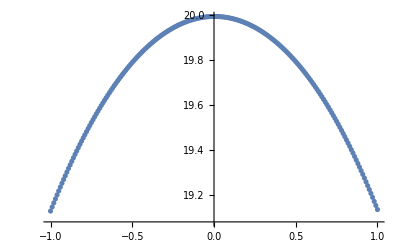

```mathematica
ListPlot[yield2]
```

```mathematica
yield3=Table[{y,dNdy[y]},{y,-.1,.1,0.01}];
```

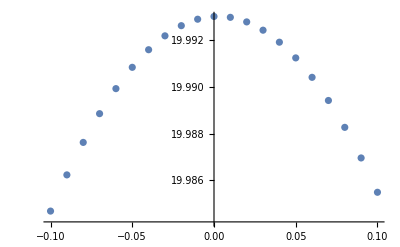

```mathematica
ListPlot[yield3]
```

```mathematica
v1[pT_]:=1/vol NIntegrate[dNd3p[pT,phi,y]*Sin[phi],{phi,0,2Pi},{y,-1,1}]
```

```mathematica
v2[pT_]:=1/vol NIntegrate[dNd3p[pT,phi,y]*Cos[phi],{phi,0,2Pi},{y,-1,1}]
```

```mathematica
v1list=Table[{pT,v1[pT]},{pT,0.01,3,0.1}];
```

```mathematica
v2list=Table[{pT,v2[pT]},{pT,0,3,0.1}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -1.27084×10^-14 and 1.76942×10^-13 for the integral and error estimates.

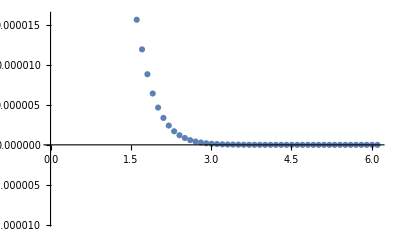

```mathematica
ListPlot[v1list]
```

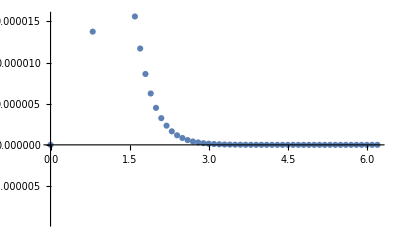

```mathematica
ListPlot[v2list]
```